◼ "\◼ "2023-11-29T03:46v1 .10M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Quantum chromodynamics and low-energy effective models

Martin Jakob Steil^1

^1Technische Universität Darmstadt

Auxiliary material and code for digram generation for Sec. 2.3 “Quantum chromodynamics and low-energy effective models” of  [M. J. Steil, - 2023 - PhD thesis]
WARNING: This notebook needs a version of the field space notebook (e.g. fs_20231206.nb) already executed — sorry that the code is not packaged jet.

Initialization

```mathematica
SetDirectory[NotebookDirectory[]];

(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

### Tagged Methods

(** Update tagged methods **)
Needs["UpdateTaggedMethod`","D:/Github/Mathematica/Packages/UpdateTaggedMethod/UpdateTaggedMethod.m"];
UpdateTaggedMethods["D:/Github/Mathematica/tagged_methods.nb"]

#### Notebook Style

```mathematica
(* NotebookHeaderUpdate | v1.1 | Update ISODateTime in NotebookHeader *)
ClearAll[NotebookHeaderUpdate];
NotebookHeaderUpdate[rule_:{}]:=Module[{header,separator},
	separator="\\[FilledSmallSquare] ";
	NotebookLocate["NB`Header"];
	(*https://mathematica.stackexchange.com/a/1411/42436*)
	header=First[FrontEndExecute[FrontEnd`ExportPacket[NotebookSelection[EvaluationNotebook[]],"PlainText"]]];
	header=StringSplit[header,separator];
	header[[1]]=StringDrop[DateString["ISODateTime"], -3];
	header=header//.rule/.{str_String/;StringContainsQ[str,"@"]:>TemplateBox[{str,"mailto:"<>str},"HyperlinkURL"]};
	header=BoxData[TemplateBox[Flatten@{"◼ ", "\"\\\◼ \"",header},"RowWithSeparators"]];
	NotebookWrite[EvaluationNotebook[],Cell[
		header,
		"NotebookHeader",
		CellTags->{"NB`Header"},
		FontFamily->"Source Sans Pro",
		FontSize->14,
		FontWeight->"Normal",
		FontSlant->"Plain"
	]]
]
NotebookHeaderUpdate::usage="NotebookHeaderUpdate[]: Update NotebookHeader using `rule` and update the ISODateTime.";
```

```mathematica
(* SetupPrintStyle | v1.0 | Setup style for notebook printout *)
SetupPrintStyle[]:=Module[{header},
	NotebookLocate["NB`Header"];
	(*https://mathematica.stackexchange.com/a/1411/42436*)
	header=First[FrontEndExecute[FrontEnd`ExportPacket[NotebookSelection[EvaluationNotebook[]],"PlainText"]]];
	
	SetOptions[EvaluationNotebook[],
		PageFooters->{
			{Cell[TextData[StyleBox[NotebookFileName[],"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}],
			None,
			Cell[TextData[StyleBox[header,"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}]},
			{Cell[TextData[StyleBox[NotebookFileName[],"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}],
			None,
			Cell[TextData[StyleBox[header,"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}]}
		},
		
		PageHeaderLines->{False,False},
		PageHeaders->{
			{Cell[
				TextData[{StyleBox[CounterBox["Page"],"PageNumber"],StyleBox["/","PageNumber"],StyleBox[CounterBox["LastPage",CounterFunction:>Identity],"PageNumber"]}],
				"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}
			],None,None},
			{Cell[
				TextData[{StyleBox[CounterBox["Page"],"PageNumber"],StyleBox["/","PageNumber"],StyleBox[CounterBox["LastPage",CounterFunction:>Identity],"PageNumber"]}],
				"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}
			],None,None}
		},
		
		PrintAction->"PrintToNotebook",
		PrintingCopies->1,
		PrintingOptions->{
			"FacingPages"->True,
			"FirstPageFace"->Right,
			"FirstPageFooter"->True,
			"FirstPageHeader"->True,
			"PageSize"->{595.32,841.92},
			"PaperOrientation"->"Portrait",
			"PaperSize"->{595.32,841.92},
			"PrintingMargins"->{{28.3465,28.3465},{50,50}}
		},
		PrintingStyleEnvironment->"Printout",
	
		ShowSyntaxStyles -> True
	]
]
```

#### Others

```mathematica
(* DefinedQ | v1.4 | Check wether a symbol is defined, i.e. has a Value, Down-, Up=, and/or OwnValues. *)
ClearAll[DefinedQ];
DefinedQ[symbol_Symbol]:=ValueQ[symbol]||DownValues[symbol]=!={}||UpValues[symbol]=!={}||OwnValues[symbol]=!={}
DefinedQ[symbol_String]:=Quiet[Check[
	ValueQ[Evaluate[Symbol[symbol]]]||DownValues[Evaluate[Symbol[symbol]]]=!={}||UpValues[Evaluate[Symbol[symbol]]]=!={}||OwnValues[Evaluate[Symbol[symbol]]] =!= {},
False], Symbol::sym]
DefinedQ[symbols_List]:=And@@Map[DefinedQ,symbols]
DefinedQ::usage="DefinedQ[symbol_]: Check wether a symbol is defined, i.e. has a Value, Down-, Up=, and/or OwnValues.";
```

```mathematica
(* AddOptions | v1.0 |  Add Option values to a symbol *)
AddOptions[x_,option_Rule]:=If[MemberQ[Options[x]/.Rule[a_,b_]:>a,option[[1]]],SetOptions[x,option],Options[x]=Join[Options[x],{option}]];
AddOptions[x_,option_List]:=AddOptions[x,#]&/@option;
AddOptions[x_,option__]:=AddOptions[x,{option}]
LookupOption::usage="AddOptions[x_,option_Rule]: Adds option to the list of Options[x].";
```

### Check for selected FS` and FRG` symbols — run fs_20231122.nb first!!

```mathematica
{
	"NCM","CM","contraction","FS`type",(*selected basics*)
	"FRG`wetterichEq`FS0","FRG`wetterichEq`FS1","FRG`wetterichEq`FS2","FRG`wetterichEq`FS3","FRG`wetterichEq`FS4", (* super field flow equations *)
	"FRG`diagramGraph","FRG`diagramCircularGraphics","FRG`diagramAxodraw2"(* Plotting utlities *)
};
If[!DefinedQ[Evaluate@%],
	MessageDialog[
		Row[{"WARNING: This notebook needs a version of the field space notebook (e.g. fs_20231122.nb) already executed — sorry that the code is not packaged jet."}],
		WindowTitle -> "Error — \"EvaluatorAbort\""
	];
	FrontEndExecute[FrontEndToken["EvaluatorAbort"]]
]
```

## 2.3.2. Asymptotic freedom, confinement, and chiral symmetry (breaking)

```mathematica
αs[q]==(2π)/((11/3 Nc-2/3 Nf)Log[q/ΛQCD])/.
{Nc->3,Nf->3,αs[q]->0.1179,q->91.19}
NSolve[%,ΛQCD]//Quiet
```

0.1179==(2 π)/(9 Log[91.19/ΛQCD])

{{ΛQCD→0.244524}}

```mathematica
(2π)/((11/3 Nc-2/3 Nf)Log[q/ΛQCD])==1/.
{Nc->3,Nf->3,ΛQCD->0.34}
NSolve[%,q]//Quiet
```

(2 π)/(9 Log[2.94118 q])==1

{{q→0.683398}}

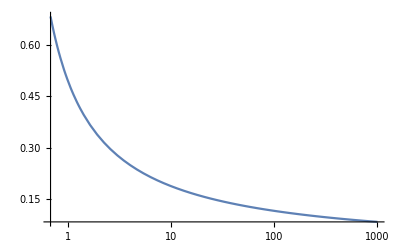

```mathematica
(2π)/((11/3 Nc-2/3 Nf)Log[q/ΛQCD])/.
{Nc->3,Nf->3,ΛQCD->0.24452365418317026};
LogLinearPlot[%,{q,0.68,1000},PlotRange->All]
```

```mathematica
4.67-2.16
```

2.51

```mathematica
1260
770*√2.
```

1260

1088.94

### PCAC and fπ - Griffith Eq. (9.7) and Burgess Eq. (9.92)

```mathematica
c0=299792458;
G=6.67408*10^-11; 
qe=1.6021766208*10^-19;
hbar=1.054571817*10^-34;

hbarcMeVfm=hbar*c0/qe/(10^6*10^-15);
```

```mathematica
Solve[Gf==(√2)/8 gw^2/MW^2,gw]
gw^2/.Last[%]
```

{{gw→-2 2^(1/4) √Gf MW},{gw→2 2^(1/4) √Gf MW}}

4 √2 Gf MW^2

```mathematica
pdgRules={Gf->1.1663788*10^-5 GeV^-2,mπ->139.57039 MeV,mμ->105.6583755MeV,θc->ArcSin[0.2243]+0*15/180*π}/.GeV->10^3 MeV
```

{Gf→(1.16638×10^-11)/MeV^2,mπ→139.57 MeV,mμ→105.658 MeV,θc→0.226225}

```mathematica
fπG^2/(π mπ^3)(gw/(4MW))^4 mμ^2(mπ^2-mμ^2)^2/.gw->2 2^(1/4) √Gf MW
```

(fπG^2 Gf^2 mμ^2 (-mμ^2+mπ^2)^2)/(8 mπ^3 π)

```mathematica
ΓG=(fπG^2 Gf^2 mμ^2 (-mμ^2+mπ^2)^2)/(8 mπ^3 π)Cos[θc]^2/.pdgRules
```

(1.45982×10^-18 fπG^2)/MeV

```mathematica
Γ=(fπ^2 Gf^2 mμ^2 (-mμ^2+mπ^2)^2)/(4 mπ^3 π)Cos[θc]^2/.pdgRules
```

(2.91964×10^-18 fπ^2)/MeV

```mathematica
ΓG/Γ
```

(0.5 fπG^2)/fπ^2

```mathematica
2.6033*10^-8*c0*10^15/hbarcMeVfm (*PDG*)
1/% MeV
Quiet@Solve[%==Γ,fπ]
```

3.95511×10^13

2.52838×10^-14 MeV

{{fπ→-93.0585 MeV},{fπ→93.0585 MeV}}

## 2.3.3. χSB and the emergence of LEFTs from QCD

### Diagram styles

```mathematica
QCD`A=FS`field["A",List[FS`type`bosonic]];

QCD`c=FS`field["c",List[FS`type`fermionic]];
QCD`cb=FS`field["c",List[FS`type`fermionic,FS`type`adjoint]];

QCD`q=FS`field["ψ",List[FS`type`fermionic]];
QCD`qb=FS`field["ψ",List[FS`type`fermionic,FS`type`adjoint]];

QCD`ϕ=FS`field["ϕ",List[FS`type`bosonic]];

QCD`fieldsSummationInformation={{QCD`A,QCD`Aidxs},{QCD`q,QCD`qidxs},{QCD`qb,QCD`qbidxs},{QCD`ϕ,QCD`ϕidxs},{QCD`c,QCD`cidxs},{QCD`cb,QCD`cbidxs}};
```

```mathematica
Options[FRG`diagramGraph]={	
	"PropagatorStyles"->{
		comp[FS`propagator[],{comp[QCD`q,μf__],μ__}]:>{Thick,GUCD`gruen},
		comp[FS`propagator[],{comp[QCD`qb,μf__],μ__}]:>{Thick,GUCD`gruen},
		comp[FS`propagator[],{comp[QCD`c,μf__],μ__}]:>{Thick,Dashed,GUCD`orange},
		comp[FS`propagator[],{comp[QCD`cb,μf__],μ__}]:>{Thick,Dashed,GUCD`orange},
		comp[FS`propagator[],{comp[QCD`A,μf__],μ__}]:>{Thick,GUCD`orange},
		comp[FS`propagator[],{comp[QCD`ϕ,μf__],μ__}]:>{Thick,GUCD`purple},
		comp[FS`propagator[],{QCD`ϕ,μ__}]:>{Thick,GUCD`senfGelb}
	},
	"NodeStyles"->{
		comp[FS`regulator[r_],{comp[q_,μf__],μ__}]:>{EdgeForm[{Thick,GUCD`gruen}],White}/;MemberQ[{QCD`qb,QCD`q},q],
		comp[FS`regulator[r_],{comp[c_,μf__],μ__}]:>{EdgeForm[{Thick,GUCD`orange}],White}/;MemberQ[{QCD`cb,QCD`c},c],		
		comp[FS`regulator[r_],{comp[QCD`A,μf__],μ__}]:>{EdgeForm[{Thick,GUCD`orange}],White},
		comp[FS`regulator[r_],{comp[QCD`ϕ,μf__],μ__}]:>{EdgeForm[{Thick,GUCD`purple}],White},
		comp[FS`vertex[],μ__]/;Count[{μ},comp[f_/;FS`type`fermionicQ[f],μf__]|f_/;FS`type`fermionicQ[f]]>2:>{EdgeForm[{Thick,Black}],GUCD`gruen},
		comp[FS`vertex[],μ__]:>{EdgeForm[{Thick,Black}],White}
	},
	"ExternalLegStyles"->{
		comp[q_,μf__]:>{Thick,GUCD`gruen}/;MemberQ[{QCD`qb,QCD`q},q]
	},
};
QCD`FRG`diagramGraphDefault=Options[FRG`diagramGraph];
```

```mathematica
FRG`diagramAxodraw2//Options={
	"widthFactor" -> 12,

	"arcedPropagator`shapes"->{
		comp[FS`propagator[],{comp[QCD`A,μf__],μ__}]:>Function[{s,r,θ1,θ2,lineStyles},
			"\\GluonArc["<>lineStyles<>"](0,0)"<>StringRiffle[ToString/@{r,θ1,If[θ2-θ1>0,θ2,θ1+360-(θ1-θ2)]},{"(",",",")"}]<>"{2}{"<>ToString[Ceiling[Axodraw2`angleDistance[θ1,θ2]*7/180]]<>"}"
		],
		comp[FS`propagator[],{comp[QCD`ϕ,μf__],μ__}]:>Function[{s,r,θ1,θ2,lineStyles},
			"\\Arc[double,"<>lineStyles<>"](0,0)"<>StringRiffle[ToString/@{r,θ1,θ2},{"(",",",")"}]
		]
	},
	
	"externalLeg`labelFunctions"->{
		comp[a_,b_]:>Function[{s,x},
			""
		]
	}
};
QCD`FRG`diagramAxodraw2Default=Options[FRG`diagramAxodraw2];
```

### ZeroPtFlow

```mathematica
List@@FRG`wetterichEq`FS0;
1/2*%;
contraction`sum[%,FS`idx,QCD`fieldsSummationInformation]//FRG`canonicalOrder//contraction`simplify;
List@@%[[2]];
QCD`Uflow=%//(LabelValues[#,"QCD`UFlow","LabelPostion"->{{Bottom,Center}}]&)

%//FRG`diagramGraph;
%//FRG`diagramCircularGraphics[#,PlotRange->3*{{-1,1},{-1,1}},ImageSize->75,"PostProcessFunction"->Function[x,GraphicsChop[x,Symmetric->False,ImagePadding->{0.04,0.04}]]]&

FRG`diagramAxodraw2`draw[%];
ParallelMap[FRG`diagramAxodraw2`compile[#,"../qcd/diagrams","qcd/diagrams"]&,%,Method->"FinestGrained"]
```

{  -  G_t_(;c_((QCD`cidxs)_0)c̄_((QCD`cbidxs)_0))∂_t R_t^(;c_((QCD`cidxs)_0)c̄_((QCD`cbidxs)_0))QCD`UFlow[[1]],  -  G_t_(;ψ_((QCD`qidxs)_0)ψ̄_((QCD`qbidxs)_0))∂_t R_t^(;ψ_((QCD`qidxs)_0)ψ̄_((QCD`qbidxs)_0))QCD`UFlow[[2]],  1/2  G_t_(;A_((QCD`Aidxs)_0)A_((QCD`Aidxs)_0))∂_t R_t^(;A_((QCD`Aidxs)_0)A_((QCD`Aidxs)_0))QCD`UFlow[[3]],  1/2  G_t_(;ϕ_((QCD`ϕidxs)_0)ϕ_((QCD`ϕidxs)_0))∂_t R_t^(;ϕ_((QCD`ϕidxs)_0)ϕ_((QCD`ϕidxs)_0))QCD`UFlow[[4]]}

{- -Graphics-,- -Graphics-,1/2 -Graphics-,1/2 -Graphics-}

{FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…]}

### λq

```mathematica
ClearAll[FRG`diagramAxodraw2`removeRegulatorInsertion];
FRG`diagramAxodraw2`removeRegulatorInsertion[FRG`diagramAxodraw2[f_,directives_List,asoc_Association]]:=Module[{R,Gs,dnew},
	R=Cases[directives,FRG`diagramAxodraw2`regulator[__]][[-1]];
	Gs=Cases[directives,FRG`diagramAxodraw2`arcedPropagator[__]];
	Gs=Select[Gs,ContainsAny[#[[-1,-1,-1]],R[[-1,2]]]&];
	Gs=Reverse@SortBy[Gs,#[[1]]&];
	dnew={FRG`diagramAxodraw2`arcedPropagator[Gs[[1,1]],Gs[[2,2]],Gs[[1,3]],Gs[[1,4]]]}~Join~Complement[directives,Flatten[{R,Gs}]];
	FRG`diagramAxodraw2[Abs@f,dnew,asoc]
]
```

```mathematica
Options[FRG`diagramCircularGraphics]={"externalLegs`radiusFactor1"->1.0,"externalLegs`labelFunction"->({}&)};
comp[FS`vertex[],{
	comp[QCD`q,idx[QCD`qidxs,0,False]],
	comp[QCD`qb,idx[QCD`qbidxs,1,False]],
	comp[QCD`q,idx[QCD`qidxs,2,False]],
	comp[QCD`qb,idx[QCD`qbidxs,3,False]]
}]
FRG`diagramCircularGraphics[%,PlotRange->3*{{-1,1},{-1,1}},ImageSize->200,"PostProcessFunction"->(GraphicsChop[#,Symmetric->False]&),Label->"QCD-4q"]
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../qcd/diagrams","qcd/diagrams"]
```

Γ̄_t^(,ψ_((QCD`qidxs)_I)ψ̄_((QCD`qbidxs)_II)ψ_((QCD`qidxs)_III)ψ̄_((QCD`qbidxs)_IV))

-Graphics-

FRG`diagramAxodraw2[…]

```mathematica
FRG`wetterichEq`FS4/.{
	FS`idx[0,False]->comp[QCD`q,idx[QCD`qidxs,0,False]],
	FS`idx[1,False]->comp[QCD`qb,idx[QCD`qbidxs,1,False]],
	FS`idx[2,False]->comp[QCD`q,idx[QCD`qidxs,2,False]],
	FS`idx[3,False]->comp[QCD`qb,idx[QCD`qbidxs,3,False]]
};
KeySortBy[FS`propagator`groupBy[Flatten@{1/2*%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
%[{5}][<|3->4|>];
contraction`sum[%,FS`idx,QCD`fieldsSummationInformation[[1;;4]]]//contraction`simplify;
QCD`λq4Flow=List@@(Total@Flatten@%);
```

```mathematica
Options[FRG`diagramCircularGraphics]={"externalLegs`radiusFactor1"->0.9,"externalLegs`radiusFactor2"->1.6,"externalLegs`labelFunction"->({}&)};
Labeled[QCD`λq4Flow[[3]],"QCD-4qFlow1"]//FRG`diagramGraph;

test=FRG`diagramCircularGraphics[%,PlotRange->3*{{-1,1},{-1,1}},ImageSize->200,"PostProcessFunction"->(GraphicsChop[#,Symmetric->False]&)]
FRG`diagramAxodraw2`removeRegulatorInsertion[%[[2]]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../qcd/diagrams","qcd/diagrams"]
```

-1/2 -Graphics-

FRG`diagramAxodraw2[…]

```mathematica
Options[FRG`diagramCircularGraphics]={"externalLegs`radiusFactor1"->0.9,"externalLegs`radiusFactor2"->1.6,"externalLegs`labelFunction"->({}&)};
Labeled[QCD`λq4Flow[[4]],"QCD-4qFlow2"]//FRG`diagramGraph;

FRG`diagramCircularGraphics[%,PlotRange->3*{{-1,1},{-1,1}},ImageSize->200,"PostProcessFunction"->(GraphicsChop[#,Symmetric->False]&)]
FRG`diagramAxodraw2`removeRegulatorInsertion[%[[2]]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../qcd/diagrams","qcd/diagrams"]
```

-1/2 -Graphics-

FRG`diagramAxodraw2[…]

```mathematica
Options[FRG`diagramCircularGraphics]={"externalLegs`radiusFactor1"->0.9,"externalLegs`radiusFactor2"->1.6,"externalLegs`labelFunction"->({}&)};
Labeled[QCD`λq4Flow[[20]],"QCD-4qFlow3"]//FRG`diagramGraph;

FRG`diagramCircularGraphics[%,PlotRange->3*{{-1,1},{-1,1}},ImageSize->200,"PostProcessFunction"->(GraphicsChop[#,Symmetric->False]&)]
FRG`diagramAxodraw2`removeRegulatorInsertion[%[[2]]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../qcd/diagrams","qcd/diagrams"]
```

-1/2 -Graphics-

FRG`diagramAxodraw2[…]

```mathematica
FRG`wetterichEq`FS4/.{
	FS`idx[0,False]->comp[QCD`q,idx[QCD`qidxs,0,False]],
	FS`idx[1,False]->comp[QCD`qb,idx[QCD`qbidxs,1,False]],
	FS`idx[2,False]->comp[QCD`q,idx[QCD`qidxs,2,False]],
	FS`idx[3,False]->comp[QCD`qb,idx[QCD`qbidxs,3,False]]
};
KeySortBy[FS`propagator`groupBy[Flatten@{1/2*%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
%[{3}][<|4->2|>];
contraction`sum[%,FS`idx,QCD`fieldsSummationInformation[[2;;3]]]//contraction`simplify;
QCD`λq2Flow=List@@(Total@Flatten@%);
```

```mathematica
Options[FRG`diagramCircularGraphics]={"externalLegs`radiusFactor1"->0.9,"externalLegs`radiusFactor2"->1.6,"externalLegs`labelFunction"->({}&)};
Labeled[QCD`λq2Flow[[-1]],"QCD-4qFlow4"]//FRG`diagramGraph;

FRG`diagramCircularGraphics[%,PlotRange->3*{{-1,1},{-1,1}},ImageSize->200,"PostProcessFunction"->(GraphicsChop[#,Symmetric->False]&)]
FRG`diagramAxodraw2`removeRegulatorInsertion[%[[2]]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../qcd/diagrams","qcd/diagrams"]
```

1/2 -Graphics-

FRG`diagramAxodraw2[…]

```mathematica
FRG`wetterichEq`FS4/.{
	FS`idx[0,False]->comp[QCD`q,idx[QCD`qidxs,0,False]],
	FS`idx[1,False]->comp[QCD`qb,idx[QCD`qbidxs,1,False]],
	FS`idx[2,False]->comp[QCD`q,idx[QCD`qidxs,2,False]],
	FS`idx[3,False]->comp[QCD`qb,idx[QCD`qbidxs,3,False]]
};
KeySortBy[FS`propagator`groupBy[Flatten@{1/2*%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
%[{4}][<|3->2,4->1|>];
contraction`sum[%,FS`idx,QCD`fieldsSummationInformation[[1;;3]]]//contraction`simplify;
QCD`λq3Flow=List@@(Total@Flatten@%);
```

```mathematica
Options[FRG`diagramCircularGraphics]={"externalLegs`radiusFactor1"->0.9,"externalLegs`radiusFactor2"->1.6,"externalLegs`labelFunction"->({}&)};
Labeled[QCD`λq3Flow[[5]],"QCD-4qFlow5"]//FRG`diagramGraph;

FRG`diagramCircularGraphics[%,PlotRange->3*{{-1,1},{-1,1}},ImageSize->200,"PostProcessFunction"->(GraphicsChop[#,Symmetric->False]&)]
FRG`diagramAxodraw2`removeRegulatorInsertion[%[[2]]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../qcd/diagrams","qcd/diagrams"]
```

-1/2 -Graphics-

FRG`diagramAxodraw2[…]